# Dormand p63

Solving the ODE from Dorman p63 different ways.

### First as a second order system typed into NDSolve.

Mathematica can numerically solve higher order ODEs directly.

```mathematica
TMax=6.192169331319640;
m=1/82.45;e=1-m;
{xSol,ySol}=NDSolveValue[{
r1=√((x[t]+m)^2+y[t]^2); r2=√((x[t]-e)^2+y[t]^2);
x''[t]==2 y'[t] +x[t] - (e(x[t]+m))/r1^3-(m(x[t]-e))/r2^3,
y''[t]==-2 x'[t] +y[t] - (e(y[t]))/r1^3-(m(y[t]))/r2^3,
x[0]==1.2,y'[0]==-1.049357509830320,y[0]==0,x'[0]==0
},
{x,y},
{t,0, TMax}
];
TabView[{
"x & y vs t"->Plot[{xSol[t],ySol[t]},{t,0, TMax},PlotLegends->{"x","y"}],
"xy"->ParametricPlot[{xSol[t],ySol[t]},{t,0,TMax}]}]
```

12

Hard to visualize like this.  An animation is better.

```mathematica
{rOrbit, rEarth, rMoon}={238,4,4};
Manipulate[Graphics[{
{LightGreen, Disk[{0,0},rOrbit]},
{Blue,Disk[({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}}).{-m rOrbit,0},rEarth]},
{Red, Point[{0,0}]},
{PointSize[0.01],Point[rOrbit*({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}}).{xSol[t],ySol[t]}]},
{Green,Disk[({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}}).{e rOrbit,0},rMoon]}
},PlotRange->1.5*rOrbit*{{-1,1},{-1,1}}],{t, 0,TMax}]
```

### First order system with a function.

Lots of ohter software will need you to rewrite to a first order system like this.

InterpolatingFunction[…]

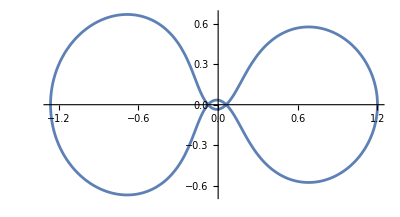

```mathematica
g[{m_,e_}][{x_,vx_,y_,vy_}]:=Module[{r1,r2},
r1=√((x+m)^2+y^2); r2=√((x-e)^2+y^2);
{vx,2 vy +x - (e(x+m))/r1^3-(m(x-e))/r2^3,
vy,-2 vx +y - (e(y))/r1^3-(m(y))/r2^3}
]
m=1/82.45;e=1-m;
u0={1.2,0,0,-1.049357509830320};
TMax=6.192169331319640;
uSol=NDSolveValue[{u'[t]==g[{m,e}][u[t]],u[0]==u0},u,{t, 0, TMax}]
ParametricPlot[uSol[t]⟦{1,3}⟧,{t,0, TMax}]
```

The Dormand book says something about the solution being unstable.  Our sensitivity tool might be helpful. The natural way to do this is as a second order system with a function.

### Second order system with a function.

I can do a second order system with a function.

```mathematica
f[{m_,e_}][{x_,y_},{vx_,vy_}]:=Module[{r1,r2},
r1=√((x+m)^2+y^2); r2=√((x-e)^2+y^2);
{2 vy +x - (e(x+m))/r1^3-(m(x-e))/r2^3,-2 vx +y - (e(y))/r1^3-(m(y))/r2^3}
]
m=1/82.45;e=1-m;
u0={1.2,0};
v0={0,-1.049357509830320};
TMax=6.192169331319640;
uSol=NDSolveValue[{u''[t]==f[{m,e}][u[t],u'[t]],u[0]==u0, u'[0]==v0},u,{t, 0, TMax}]
ParametricPlot[uSol[t],{t,0, TMax}]
```

InterpolatingFunction[…]

-Graphics-

The sensitivities with respect to the initial conditions are the same as before. If 
	y''=f(y,y')  and y(0)=x  and y'(0)=v
then Jx=∂_x y  and Jv=∂_v y satisfy
	Jx'' | = | ∂_1 f.Jx | + | ∂_2 f.Jx'
Jy'' | = | ∂_1 f.Jy | + | ∂_2 f.Jy'
with initial conditions
	Jx(0)=Id and Jx'(0)=0
	Jy(0)=0  and Jy'(0)=Id
These are easy enough to compute and solve.

```mathematica
Clear[m,e]
d2f[{m_,e_}][{x_,y_},{vx_,vy_}]:={{0,2},{-2,0}}
d1f[{m_,e_}][{x_,y_},{vx_,vy_}]:=Module[{r1,r2,dr1,dr2},
r1=√((x+m)^2+y^2);dr1={m+x,y}/r1;
r2=√((x-e)^2+y^2);dr2={x-e,y}/r2;
(1-e/r1^3-m/r2^3)*({{1, 0}, {0, 1}})
+(3e)/r1^4 KroneckerProduct[{x+m,y},dr1]
+(3m)/r2^4 KroneckerProduct[{x-e,y},dr2]
]
```

The first question is: How do I check these are correct? In Mathematica I can just ask!

```mathematica
{D[f[{m,e}][{x,y},{vx,vy}],{{x,y}}]==d1f[{m,e}][{x,y},{vx,vy}],
D[f[{m,e}][{x,y},{vx,vy}],{{vx,vy}}]==d2f[{m,e}][{x,y},{vx,vy}]}
```

{True,True}

In less symbolic languages I would probably be forced to look at numerical values.  We can make a pretty convincing  plot using the tangent line idea.

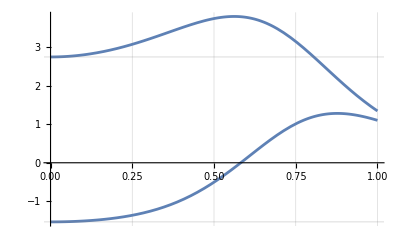

```mathematica
{m,e}=RandomReal[{0,1},2];
{xy,vxy}=RandomReal[{-1,1},{2,2}];
h=RandomReal[{-1,1},2];
Plot[(f[{m,e}][xy+ϵ h,vxy]-f[{m,e}][xy-ϵ h,vxy])/(2ϵ),{ϵ,10^-7,1},
GridLines->{Automatic,d1f[{m,e}][xy,vxy].h}]
```

Seeing the error behave appropriately is more convincing.

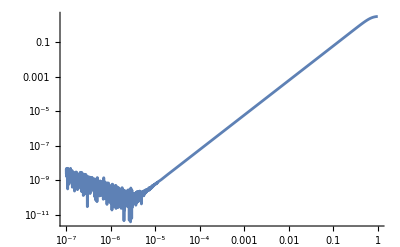

```mathematica
LogLogPlot[ {
Norm[d1f[{m,e}][xy,vxy].h-(f[{m,e}][xy+ϵ h,vxy]-f[{m,e}][xy-ϵ h,vxy])/(2ϵ)]
},
{ϵ,10^-7,1}]
```

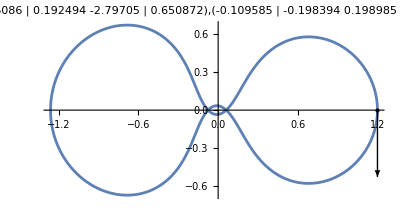

```mathematica
m=1/82.45;e=1-m;
u0={1.2,0};
v0={0,-1.049357509830320};
TMax=6.192169331319640;
{uSol,JxSol, JvSol}=NDSolveValue[{
u''[t]==f[{m,e}][u[t],u'[t]],
u[0]==u0, u'[0]==v0,
Jx''[t]==d1f[{m,e}][u[t],u'[t]].Jx[t]+d2f[{m,e}][u[t],u'[t]].Jx'[t],
Jx[0]==({{1, 0}, {0, 1}}),Jx'[0]==({{0, 0}, {0, 0}}),
Jv''[t]==d1f[{m,e}][u[t],u'[t]].Jv[t]+d2f[{m,e}][u[t],u'[t]].Jv'[t],
Jv[0]==({{0, 0}, {0, 0}}),Jv'[0]==({{1, 0}, {0, 1}})
},{u,Jx,Jv},{t, 0, TMax}];
ParametricPlot[uSol[t],{t,0, TMax},
Epilog->{Point[u0],Arrow[{u0,u0+0.5v0}]},
PlotLabel->Map[MatrixForm,{JxSol[TMax],JvSol[TMax]}]
]
```